```mathematica
Quit[];
```

```mathematica
alpha = 0.02230776697175726;
beta =Pi/20;
x1 = {0.01,0,0};
x2 = {Tan[beta]+0.01,1,Tan[alpha]};
x0 = {0,y,z};
ϕ1 = Norm[Cross[x2  -x1,x1-x0]]/Norm[x2-x1];
sol1 = FullSimplify[Solve[ϕ1* ϕ1==0.0165*0.0165,z]];

sol1[[1,1,2]]/.y->t;
sol1[[2,1,2]]/.y->t;
a1 = ParametricPlot3D[{x=0,y=t,z=sol1[[1,1,2]]/.y->t},{t,0,0.5},PlotRange->{{-0.1,0.1},{-0.1,0.1},{-0.1,0.1}}];
a2 = ParametricPlot3D[{x=0,y=t,z=sol1[[2,1,2]]/.y->t},{t,0,0.5},PlotRange->{{-0.1,0.1},{-0.1,0.1},{-0.1,0.1}}];
```

```mathematica
Show[a2]
```

-Graphics3D-

```mathematica
x1 = {-0.01,0,0};
x2 = {Tan[-beta]-0.01,1,Tan[alpha]};
x0 = {0,y,z};
 ϕ2 = Norm[Cross[x2  -x1,x1-x0]]/Norm[x2-x1]
ϕ1*ϕ1
ϕ2*ϕ2
a = Plot3D[ϕ1* ϕ1==0.0165*0.0165,{y,0,1},{z,0,1}]
b = Plot3D[ϕ2* ϕ2==0.0165*0.0165,{y,0,1},{z,0,1}]
```

0.999751 √(0.00010005+Abs[0.0223115 y-1. z]^2)

0.999502 (0.00010005+Abs[0.0223115 y-1. z]^2)

0.999502 (0.00010005+Abs[0.0223115 y-1. z]^2)

-Graphics3D-

-Graphics3D-

```mathematica
b= Plot3D[ϕ2* ϕ2==0.014*0.014,{y,0,1},{z,0,1}]

rod1 = ParametricPlot3D[{x=t*Tan[beta]+0.01,y=t,z=t*Tan[alpha]},{t,-5,5},PlotRange->{{-0.1,0.1},{-0.1,0.1},{-0.1,0.1}}];
rod2= ParametricPlot3D[{x=-t*Tan[beta]-0.01,y=t,z=t*Tan[alpha]},{t,-5,5},PlotRange->{{-0.1,0.1},{-0.1,0.1},{-0.1,0.1}}];
sphere = Graphics3D[Sphere[{ 0,0,0.016},0.02],PlotRange->{{-0.1,0.1},{-0.1,0.1},{-0.1,0.1}}];

Show[rod1,rod2,sphere];
Show[rod1,a1,a2,rod2]
```

-Graphics3D-

-Graphics3D-

{{z→5.24094×10^-16 (-1.86997×10^13+4.25715×10^13 y)},{z→5.24094×10^-16 (1.86997×10^13+4.25715×10^13 y)}}

Plot3D[{y},{y,0,1}]

```mathematica
m = 0.3;
r = 0.014;
alpha = 0.02230776697175726;
beta =0;
g = 9.8;

q={{y[t],z[t]}};
dq = D[q,t];
ddq=D[dq,t];


dy=D[y[t],t];
dz=D[z[t],t];

PE=m*g*(z[t]);
KE=1/2 m*y'[t]^2 + 1/2 m*z'[t]^2;
L = FullSimplify[KE-PE];

InitCon={x'[0]==xin, x[0]==xdin}
sol = NDSolve[Join[EL,InitCon],{x},{t,0,10}];
```

```mathematica
Quit[];
```

```mathematica
Ndsolve[xin_, xdin_,tstart_,tperiod_,thetain_]:=Module[{z,dzdx,P,Q,x,matr,beta,eq1,InitCon,EL,sol,xsol,xdsol,theta},
z[t] = Sqrt[(R+r)^2-Cos[theta[t]]^2*(d0+(x[t]*Tan[theta[t]]))^2];
dzdx =D[z[t],x[t]];
P = J*Rr^2 *x'[t]*D[z[t],t]*z[t]^-3;
Q = D[D[z[t],t],t]-x''[t]*D[z[t],x[t]];
matr =J*Rr^2*z[t]^-2+m*(1+(dzdx)^2); 
     eq1= (-m*g*Sin[alpha]+P-m*dzdx*(g*Cos[alpha]+Q))/matr;
beta'[t] = x'[t]*Rr/z[t];
R=12.6*10^-3;
r=3.1*10^-3;
d0=9.4*10^-3;
J=1.32*10^-6;
Rr=(R+r)/R;
m=20.8*10^-3;
g=9.8;
alpha=0.035;
theta[t] = thetain;
theta'[t]=0;
theta''[t] = 0;
EL={x''[t]==eq1};
InitCon={x'[tstart]==xdin, x[tstart]==xin};
sol = NDSolve[Join[EL,InitCon],{x},{t,tstart,tperiod+tstart}];
xsol=x/.sol[[1]];
xdsol=x'/.sol[[1]];
Return[{xsol[tperiod+tstart],xdsol[tperiod+tstart],xsol}];
];
T[xin_, xddin_]:=Module[{z,dzdx,matr,eq1,sol,x,theta}, 
z = Sqrt[(R+r)^2-Cos[theta]^2*(d0+(x*Tan[theta]))^2];
dzdx =D[z,x];
matr =J*Rr^2*z^-2+m*(1+(dzdx)^2);
eq1 =(-m*g*Sin[alpha]-m*dzdx*g*Cos[alpha])/matr==0.01;
R=12.6*10^-3;
r=3.1*10^-3;
d0=9.4*10^-3;
J=1.32*10^-6;
Rr=(R+r)/R;
m=20.8*10^-3;
g=9.8;
alpha=0.035;
x = xin;
sol=FindRoot[(-m*g*Sin[alpha]-m*dzdx*g*Cos[alpha])/matr==xddin,{theta,0}];
Return[sol[[1,2]]];
];
```

{0.000191687,0.0183375,InterpolatingFunction[{{0., 0.01}}, <>]}

{0.000366752,0.0166755,InterpolatingFunction[{{0.01, 0.02}}, <>]}

Piecewise[{{InterpolatingFunction[{{0., 0.01}}, <>], t<0.01}, {InterpolatingFunction[{{0.01, 0.02}}, <>], t≥0.01}, {0, True}}]

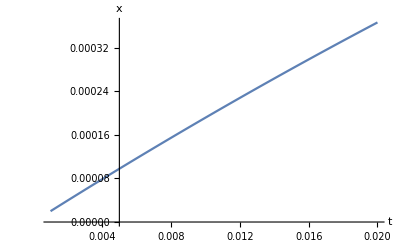

0.0362075

```mathematica
{xr,xdr,xsolr1}=Ndsolve[0,0.02,0,0.01,0.01]
{xr,xdr,xsolr2}=Ndsolve[xr,xdr,0+0.01,0.01,0.01]

t1 = 0.01;
θ1sol=Piecewise[{{xsolr1,t<0.01} ,{xsolr2,t≥0.01}}]
Plot[θ1sol[t],{t,0.001,0.02},AxesLabel->{t,x}]

thetasol = T[0.1,0.08]
```

```mathematica
tperiod = 0.01;
kp = 2;
kd = 3;
period1 = 12; (*sec*)
w1= 2*Pi/period1;
period2 = 4; (*sec*)
w2= 2*Pi/period2;
xref = 0.1*Sin[w1*t];
xref2 =- 0.005*Sin[w2*t]+0.1;
(*xref = 0.1*t;*)

dxref = D[xref,t];
dxref2 = D[xref2,t];
time = 0;
xfed=xref/.t->time;
xdfed=dxref/.t->time;


(*Plot[xref,{t,0,5}]
Plot[dxref,{t,0,5}]*)
a = 1;
θ1sol= 0

Do[
If[time<=3,{xrefinput=xref/.t->time,
xdrefinput=dxref/.t->time},{time1 = time -3,xrefinput=xref2/.t->time1,
xdrefinput=dxref2/.t->time1}];

xddinput = kp*(xrefinput-xfed)+kd*(xdrefinput-xdfed);
thetasol = T[xfed,xddinput];
Print[thetasol];

{xr,xdr,xsolr1}=Ndsolve[xfed,xdfed,time,tperiod,thetasol];(*xin_, xdin_,tstart_,tperiod_,thetain_*)
xfed  = xr;
xdfed = xdr;
θ1sol=Piecewise[{{θ1sol,t<time} ,{xsolr1,t≥time}}];
time  = time +0.01;
,{1200}]
```

0

12.

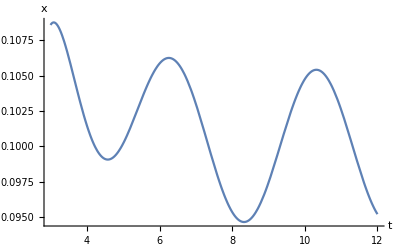

```mathematica
time
Plot[θ1sol[t],{t,3,12},AxesLabel->{t,x}]
(*Plot[xref2,{t,0,time},AxesLabel->{t,x}]*)
```

```mathematica
tperiod = 0.01;
kp = 2;
kd = 3;
period = 10; (*sec*)
w = 2*Pi/period;
xref = 0.20;
dxref = D[xref,t];
time = 0;
xfed=0;
xdfed=dxref/.t->time;
(*Plot[xref,{t,0,5}]
Plot[dxref,{t,0,5}]*)
a = 1;
θ1sol= 0

Do[
xrefinput=xref/.t->time;
xdrefinput=dxref/.t->time;
xddinput = kp*(xrefinput-xfed)+kd*(xdrefinput-xdfed);
thetasol = 0.02385-0.478 (-xref+xfed)-0.506 xdfed;
Print[thetasol];
{xr,xdr,xsolr1}=Ndsolve[xfed,xdfed,time,tperiod,thetasol];(*xin_, xdin_,tstart_,tperiod_,thetain_*)
xfed  = xr;
xdfed = xdr;
θ1sol=Piecewise[{{θ1sol,t<time} ,{xsolr1,t≥time}}];
time  = time +0.01;
,{500}]
```

0

0.14335
0.141205
0.139084
0.136986
0.134908
0.132849
0.130809
0.128785
0.126778
0.124787
0.122811
0.120849
0.118902
0.116968
0.115049
0.113144
0.111254
0.109377
0.107516
0.105669
0.103838
0.102023
0.100224
0.0984414
0.0966765
0.0949295
0.0932009
0.0914913
0.0898012
0.0881312
0.0864817
0.0848534
0.0832466
0.0816618
0.0800994
0.0785598
0.0770434
0.0755504
0.0740812
0.0726358
0.0712146
0.0698177
0.068445
0.0670968
0.065773
0.0644736
0.0631985
0.0619477
0.0607209
0.0595181
0.0583391
0.0571837
0.0560516
0.0549426
0.0538564
0.0527927
0.0517513
0.0507318
0.0497339
0.0487573
0.0478017
0.0468668
0.0459521
0.0450575
0.0441825
0.0433269
0.0424903
0.0416724
0.0408729
0.0400915
0.0393279
0.0385818
0.0378529
0.0371409
0.0364456
0.0357667
0.0351039
0.034457
0.0338258
0.0332099
0.0326092
0.0320234
0.0314524
0.0308957
0.0303534
0.0298251
0.0293106
0.0288097
0.0283223
0.027848
0.0273867
0.0269383
0.0265024
0.026079
0.0256677
0.0252685
0.024881
0.0245052
0.0241408
0.0237876
0.0234455
0.0231141
0.0227934
0.0224831
0.0221831
0.0218931
0.021613
0.0213425
0.0210815
0.0208298
0.0205871
0.0203533
0.0201282
0.0199116
0.0197033
0.0195031
0.0193109
0.0191264
0.0189494
0.0187797
0.0186173
0.0184618
0.0183132
0.0181712
0.0180356
0.0179063
0.0177831
0.0176658
0.0175542
0.0174483
0.0173477
0.0172524
0.0171622
0.0170769
0.0169964
0.0169205
0.016849
0.0167818
0.0167188
0.0166598
0.0166047
0.0165533
0.0165054
0.016461
0.01642
0.0163821
0.0163473
0.0163155
0.0162864
0.0162601
0.0162363
0.016215
0.0161961
0.0161794
0.0161649
0.0161524
0.0161418
0.0161332
0.0161262
0.016121
0.0161173
0.0161152
0.0161144
0.016115
0.0161169
0.0161199
0.0161241
0.0161293
0.0161354
0.0161425
0.0161505
0.0161592
0.0161687
0.0161789
0.0161897
0.0162011
0.016213
0.0162254
0.0162382
0.0162514
0.0162651
0.016279
0.0162932
0.0163077
0.0163224
0.0163372
0.0163523
0.0163675
0.0163827
0.0163981
0.0164135
0.016429
0.0164445
0.0164599
0.0164754
0.0164908
0.0165062
0.0165215
0.0165367
0.0165518
0.0165669
0.0165818
0.0165966
0.0166112
0.0166257
0.0166401
0.0166543
0.0166683
0.0166822
0.0166959
0.0167094
0.0167228
0.016736
0.0167489
0.0167617
0.0167743
0.0167868
0.016799
0.016811
0.0168229
0.0168345
0.016846
0.0168572
0.0168683
0.0168792
0.0168899
0.0169004
0.0169108
0.0169209
0.0169309
0.0169407
0.0169503
0.0169597
0.016969
0.0169781
0.016987
0.0169958
0.0170044
0.0170128
0.0170211
0.0170292
0.0170372
0.017045
0.0170527
0.0170602
0.0170676
0.0170748
0.017082
0.017089
0.0170958
0.0171025
0.0171091
0.0171156
0.017122
0.0171282
0.0171343
0.0171404
0.0171463
0.0171521
0.0171578
0.0171634
0.0171688
0.0171742
0.0171795
0.0171847
0.0171898
0.0171949
0.0171998
0.0172046
0.0172094
0.0172141
0.0172187
0.0172232
0.0172277
0.017232
0.0172363
0.0172406
0.0172447
0.0172488
0.0172528
0.0172568
0.0172607
0.0172645
0.0172683
0.017272
0.0172757
0.0172793
0.0172828
0.0172863
0.0172897
0.0172931
0.0172964
0.0172997
0.017303
0.0173062
0.0173093
0.0173124
0.0173154
0.0173184
0.0173214
0.0173243
0.0173272
0.0173301
0.0173329
0.0173356
0.0173384
0.017341
0.0173437
0.0173463
0.0173489
0.0173515
0.017354
0.0173565
0.0173589
0.0173613
0.0173637
0.0173661
0.0173684
0.0173707
0.017373
0.0173752
0.0173775
0.0173796
0.0173818
0.0173839
0.0173861
0.0173881
0.0173902
0.0173922
0.0173943
0.0173963
0.0173982
0.0174002
0.0174021
0.017404
0.0174059
0.0174077
0.0174096
0.0174114
0.0174132
0.017415
0.0174167
0.0174185
0.0174202
0.0174219
0.0174236
0.0174252
0.0174269
0.0174285
0.0174301
0.0174317
0.0174333
0.0174348
0.0174364
0.0174379
0.0174394
0.0174409
0.0174424
0.0174439
0.0174453
0.0174468
0.0174482
0.0174496
0.017451
0.0174524
0.0174537
0.0174551
0.0174564
0.0174577
0.017459
0.0174603
0.0174616
0.0174629
0.0174642
0.0174654
0.0174666
0.0174679
0.0174691
0.0174703
0.0174715
0.0174726
0.0174738
0.017475
0.0174761
0.0174772
0.0174784
0.0174795
0.0174806
0.0174817
0.0174827
0.0174838
0.0174849
0.0174859
0.017487
0.017488
0.017489
0.01749
0.017491
0.017492
0.017493
0.017494
0.0174949
0.0174959
0.0174968
0.0174978
0.0174987
0.0174996
0.0175005
0.0175014
0.0175023
0.0175032
0.0175041
0.017505
0.0175058
0.0175067
0.0175075
0.0175084
0.0175092
0.01751
0.0175108
0.0175116
0.0175124
0.0175132
0.017514
0.0175148
0.0175156
0.0175163
0.0175171
0.0175178
0.0175186
0.0175193
0.0175201
0.0175208
0.0175215
0.0175222
0.0175229
0.0175236
0.0175243
0.017525
0.0175257
0.0175263
0.017527
0.0175277
0.0175283
0.017529
0.0175296
0.0175302
0.0175309
0.0175315
0.0175321
0.0175327
0.0175333
0.0175339
0.0175345
0.0175351
0.0175357
0.0175363
0.0175369
0.0175374
0.017538
0.0175386
0.0175391
0.0175397
0.0175402
0.0175408
0.0175413
0.0175418
0.0175423
0.0175429
0.0175434
0.0175439
0.0175444
0.0175449
0.0175454
0.0175459
0.0175464
0.0175469
0.0175473
0.0175478
0.0175483
0.0175487
0.0175492
0.0175497
0.0175501
0.0175506
0.017551
0.0175515
0.0175519
0.0175523
0.0175528
0.0175532
0.0175536
0.017554
0.0175544
0.0175548
0.0175553
0.0175557
0.0175561
0.0175565
0.0175568

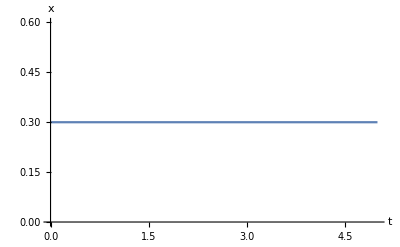

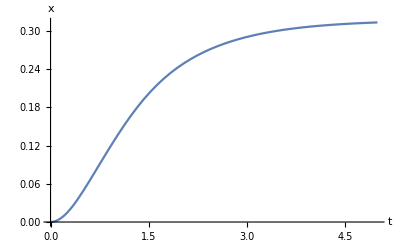

```mathematica
Plot[xref,{t,0,time},AxesLabel->{t,x}]
Plot[θ1sol[t],{t,0,time},AxesLabel->{t,x}]
```